```mathematica
Clear["Global`*"]
NotebookSave[]
Options[Domains]={DeltaT->None,TotalT->None,DeltaF->None,TotalF->None,Toffset->0,Centered->False,OnlyParameters->False};

Domains[n_,opts___]:=Module[{tos,Ts,Ttot,Fs,Ftot,centered,param,timedomain,frequencydomain},
(*Aignacion opciones*)
Ts=DeltaT/. {opts}/. Options[Domains];
Ttot=TotalT/. {opts}/. Options[Domains];
Fs=DeltaF/. {opts}/. Options[Domains];
Ftot=TotalF/. {opts}/. Options[Domains];
tos=Toffset/. {opts}/. Options[Domains];
centered=Centered/. {opts}/. Options[Domains];
param=OnlyParameters/. {opts}/. Options[Domains];

Switch[First[Flatten[Position[N[{Ts,Ttot,Fs,Ftot,tos}],_?NumberQ]]],1,Ttot=n Ts;Fs=1/Ttot;Ftot=1/Ts,2,Ts=Ttot/n;Fs=1/Ttot;Ftot=1/Ts,3,Ts=1/(n Fs);Ttot=1/Fs;Ftot=n Fs,4,Ts=1/Ftot;Ttot=n Ts;Fs=Ftot/n,_,Ts=1;Ttot=n;Fs=1/n;Ftot=1];
If[param,Return[{Ts,Ttot,Fs,Ftot}],timedomain=tos+(Range[n]-1)Ts;
frequencydomain=If[centered,(Range[n]-Ceiling[n/2])Fs,(Range[n]-1)Fs];
Return[{timedomain,frequencydomain}]]]

Options[AddSignalRange]={Toffset->0};

AddSignalRange[data_List,opts___]:=Transpose[{Domains[Length[data],opts][[1]],data}]

Options[AddSpectrumRange]={Centered->False,HalfSpectrum->False};

AddSpectrumRange[data_List,opts___]:=Module[{n,lista,half,centered},half=HalfSpectrum/. {opts}/. Options[AddSpectrumRange];
If[half,centered=False,centered=Centered/. {opts}/. Options[AddSpectrumRange];];
n=Length[data];
lista=If[centered,Transpose[{Domains[n,Centered->True,opts][[2]],RotateRight[data,Ceiling[n/2]-1]}],Transpose[{Domains[n,Centered->False,opts][[2]],data}]];
If[half,(*then centered is forced to False*)Take[lista,{1,Ceiling[(n+1)/2]}],lista (*can be centered or not*)]]
-Graphics-;
-Graphics-;
```

1/50

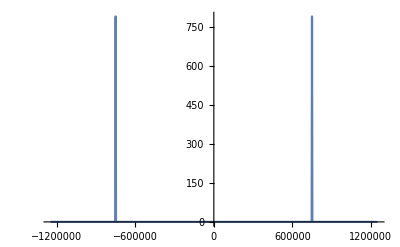

√(π/2) DiracDelta[-30000 π+w]+√(π/2) DiracDelta[30000 π+w]

1/2 DiracDelta[-30000 π+w]+1/2 DiracDelta[30000 π+w]

π DiracDelta[-30000 π+w]+π DiracDelta[30000 π+w]

π DiracDelta[-30000 π+w]+π DiracDelta[30000 π+w]

1/2 DiracDelta[-15000+w]+1/2 DiracDelta[15000+w]

DiracDelta[-15000+w]/(2 √(2 π))+DiracDelta[15000+w]/(2 √(2 π))

1/4 (1-√5)

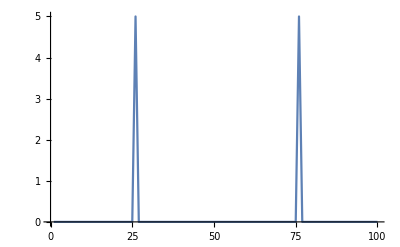

79.5775

```mathematica
fs = 50000;
ps = 1/fs;
np = 1000;
modulante[t_]:= Cos[2*Pi*15000*t];
portadora[t_]:= Cos[2*Pi*200*10^6*t];
Clear[datosModulante]
datosModulante = Table[modulante[t],{t,0,(np-1)*ps,ps}];
tiempomedido = Length[datosModulante]*ps
espectroModulante = AddSpectrumRange[Abs[Fourier[datosModulante]],TotalF -> fs,Centered-> True];
ListLinePlot[espectroModulante/tiempomedido,PlotRange->Full]
FourierTransform[modulante[t],t,w,FourierParameters->{0, 1}] (*Default, Frecuencia angular (√(π/2) )*)
FourierTransform[modulante[t],t,w,FourierParameters->{-1, 1}](* Data Analysis, Frecuencia angular (1/2)*)
FourierTransform[modulante[t],t,w,FourierParameters->{1, 1}](*Comun en bibliografia, Frecuencia angular  (π)*)
FourierTransform[modulante[t],t,w,FourierParameters->{1, -1}](*Signal Processing, Frecuencia angular  (π)*)
FourierTransform[modulante[t],t,w,FourierParameters->{0, -2Pi}](*Signal processing and electrical engineering, Frecuencia (hz) (1/2)*)
FourierTransform[modulante[t],t,w,FourierParameters->{-1,-2Pi}](*Signal processing and electrical engineering, Frecuencia (hz) (1/(2 √(2π)))*)
Last[datosModulante]
```